```mathematica
mySqrt[X_]:=-I*Sqrt[-X];
```

```mathematica
1/(-e+ⅈ n-c o+z)/.{o->p/(1+p/(Sqrt[(z+n*I-J)^2-q^2]))}
```

1/(-e+ⅈ n+z-(c p)/(1+p/(√(-q^2+(-J+ⅈ n+z)^2))))

```mathematica
1/(-e+ⅈ n+z-(c p)/(1+p/(√(-q^2+(-J+ⅈ n+z)^2))))/.{e->J+q*Cos[k]}
```

```mathematica
1/(-J+ⅈ n+z-(c p)/(1+p/(√(-q^2+(-J+ⅈ n+z)^2)))-q Cos[k])
1/(-J+ⅈ n+z-(c p)/(1+p/(√(-q^2+(-J+ⅈ n+z)^2)))-q Cos[k])/.{J->1, p->-0.1, q->0.1, c->0.01}
```

1/(-1+ⅈ n+z+0.001/(1-0.1/(√(-0.01+(-1+ⅈ n+z)^2)))-0.1 Cos[k])

```mathematica
1/(-1+ⅈ n+z+0.001/(1-0.1/(√(-0.010000000000000002+(-1+ⅈ n+z)^2)))-0.1 Cos[k])/.{n->0.0001}
```

1/((-1.+0.0001 ⅈ)+0.001/(1-0.1/(√(-0.01+((-1.+0.0001 ⅈ)+z)^2)))+z-0.1 Cos[k])

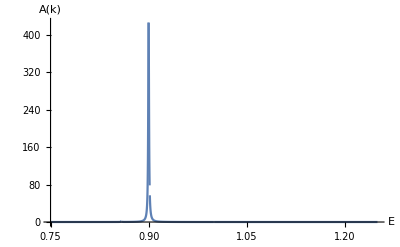

```mathematica
Plot[{-1/( Pi)Im[1/((-0.9+0.0007ⅈ)+0.0001/(1-0.1/mySqrt[-0.010000000000000002+((-1.+0.0007ⅈ)+z)^2])+z)]},{z,0.75,1.25},AxesLabel->{"E","A(k)"},PlotRange->All]
```

```mathematica
DensityPlot[-1/Pi Im[1/((-1.+0.006 ⅈ)+0.001/(1-0.1/mySqrt[-0.010000000000000002+((-1.+0.006 ⅈ)+z)^2])+z-0.1 Cos[k])],{k,0,2*Pi}, {z,0.75,1.25},AxesLabel->{"k","E"}, Exclusions->None, PlotLegends->Automatic, ColorFunction->(ColorData["AvocadoColors"][Log[1+#]/Log[20]]&), ColorFunctionScaling->False, PlotRange->All,PlotPoints->420]
```

-Graphics-